```mathematica
Needs["MFGraphs`"]
```

```mathematica
Cases[$Packages,"MFGraphs`"]
```

{MFGraphs`}

```mathematica
Names["MFGraphs`*"]
```

{AtHead,AtTail,DataToEquations,DataToGraph,EE,F,Intg,j,m,OtherWay,Parameters,RR,TransitionsAt,triple2path,usage,UU,x}

```mathematica
Get["MFGraphs`Examples`ExamplesParameters`"];
Get["MFGraphs`Examples`ExamplesData`"];
Test[17]
```

{{1,2,3,4},{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},{{1,2}},{{3,2},{4,1}},{}}

```mathematica
Get["MFGraphs`Examples`IterationFunction`"]
```

AssociationThread::invrk: The argument {{1->2,-jvars[{1,1->2}]+jvars[{2,1->2}]},{2->3,-jvars[{2,2->3}]+jvars[{3,2->3}]},{2->4,-jvars[{2,2->4}]+jvars[{4,2->4}]}} is not a valid rule.

AssociationThread::invrk: The argument {#→-uvars[{1,1->2}]+uvars[{2,1->2}]-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][1->2],#→-uvars[{2,2->3}]+uvars[{3,2->3}]-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][2->3],#→-uvars[{2,2->4}]+uvars[{4,2->4}]-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][2->4]} is not a valid rule.

AssociationThread::invrk: The argument {#→-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][1->2]+Intg AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][1->2],#→-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{«1»,«1»},{DirectedEdge[«2»],Plus[«2»]}}][«1»]+«1»,#→-AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][2->4]+Intg AssociationThread[{{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]},{DirectedEdge[«2»],Plus[«2»]}}][2->4]} is not a valid rule.

General::stop: Further output of AssociationThread::invrk will be suppressed during this calculation.

$Aborted

```mathematica
Data=DataG[26];
```

```mathematica
MFGEquations=DataToEquations[Data];
```

```mathematica
SameQ[Equal,Equal]
```

True

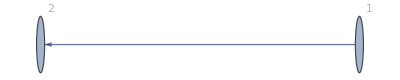
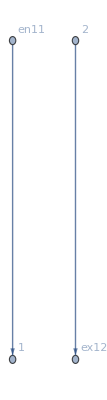
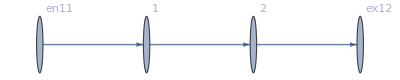
<|BG→-Graphics-,EntranceVertices→{1},InwardVertices→<|1→en11|>,InEdges→{en11->1},ExitVertices→{2},OutwardVertices→<|2→ex12|>,OutEdges→{2->ex12},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2},EL→{1->2,2->ex12,en11->1},BEL→{1->2},FVL→{1,2,en11,ex12},AllTransitions→{{1,1->2,en11->1},{1,en11->1,1->2},{2,1->2,2->ex12},{2,2->ex12,1->2}},IncomingEdges→MFGraphs`Private`IncomingEdges$5270,OutgoingEdges→MFGraphs`Private`OutgoingEdges$5270,NoDeadEnds→{{1,1->2},{1,en11->1},{2,1->2},{2,2->ex12}},NoDeadStarts→{{2,1->2},{en11,en11->1},{1,1->2},{ex12,2->ex12}},jargs→{{2,1->2},{ex12,2->ex12},{1,en11->1},{1,1->2},{2,2->ex12},{en11,en11->1}},js→{j13,j14,j15,j16,j17,j18},jvars→<|{2,1->2}→j13,{ex12,2->ex12}→j14,{1,en11->1}→j15,{1,1->2}→j16,{2,2->ex12}→j17,{en11,en11->1}→j18|>,jts→{jt19,jt20,jt21,jt22},jtvars→<|{1,1->2,en11->1}→jt19,{1,en11->1,1->2}→jt20,{2,1->2,2->ex12}→jt21,{2,2->ex12,1->2}→jt22|>,uargs→{{1,1->2},{2,2->ex12},{en11,en11->1},{2,1->2},{ex12,2->ex12},{1,en11->1}},us→{u23,u24,u25,u26,u27,u28},uvars→<|{1,1->2}→u23,{2,2->ex12}→u24,{en11,en11->1}→u25,{2,1->2}→u26,{ex12,2->ex12}→u27,{1,en11->1}→u28|>,CurrentCompCon→MFGraphs`Private`CurrentCompCon$5270,EqCurrentCompCon→(j16==0||j13==0)&&(j17==0||j14==0)&&(j18==0||j15==0),TransitionCompCon→MFGraphs`Private`TransitionCompCon$5270,EqTransitionCompCon→(jt19==0||jt20==0)&&(jt21==0||jt22==0),Compu→MFGraphs`Private`Compu$5270,EqCompCon→jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqAllComp→(j16==0||j13==0)&&(j17==0||j14==0)&&(j18==0||j15==0)&&(jt19==0||jt20==0)&&(jt21==0||jt22==0)&&jt19==0&&(jt20==0||-u23+u28==0)&&(jt21==0||-u24+u26==0)&&jt22==0,EqPosCon→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22],CurrentSplitting→MFGraphs`Private`CurrentSplitting$5270,CurrentGathering→MFGraphs`Private`CurrentGathering$5270,EqBalanceSplittingCurrents→j16==jt19&&j15==jt20&&j13==jt21&&j17==jt22,EqBalanceGatheringCurrents→j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21,EntryArgs→{{1,en11->1}},EntryDataAssociation→<|{1,en11->1}→1|>,EqEntryIn→j15==1,NonZeroEntryCurrents→True,ExitCosts→<|ex12→2|>,ExitValues→MFGraphs`Private`ExitValues$5270,EqExitValues→u27==2,SwitchingCosts→<|{1,1->2,en11->1}→∞,{1,en11->1,1->2}→0,{2,1->2,2->ex12}→0,{2,2->ex12,1->2}→∞,{2,2->ex12,2->ex12}→∞,{2,2->ex12,en11->1}→∞,{1,en11->1,en11->1}→∞|>,OutRules→{{2,2->ex12,1->2}→∞,{2,2->ex12,2->ex12}→∞,{2,2->ex12,en11->1}→∞},InRules→{{1,1->2,en11->1}→∞,{1,en11->1,en11->1}→∞},Transu→MFGraphs`Private`Transu$5270,EqSwitchingConditions→u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24,EqValue→MFGraphs`Private`EqValue$5270,EqValueAuxiliaryEdges→-u25+u28==0&&-u24+u27==0,EqAll→NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22]&&j16==jt19&&j15==jt20&&j13==jt21&&j17==jt22&&j13==jt20&&j18==jt19&&j16==jt22&&j14==jt21&&j15==1&&u27==2&&u28≤u23&&u23≤∞&&u24≤∞&&u26≤u24&&-u25+u28==0&&-u24+u27==0|>

```mathematica
MFGEquations
```

```mathematica
MakeWord[.....
```

```mathematica
CriticalCongestionSolve[MFGEquations_Association]:= Module[{variables},Reduce.... Just return the solution (us, js, jts)];
```

```mathematica
Reformat results from above function:
```

```mathematica
Compi
```

```mathematica
jays=AssociationThread[MFGEquations["BEL"],(MFGEquations["jvars"][AtHead[#]]-MFGEquations["jvars"][AtTail[#]]&)/@MFGEquations["BEL"]];
```

```mathematica
Parameters
```

<|alpha→1,beta→2,g[m]→g$21565,W[x,A]→W$21565,V[x]→V$21565,H[x,p,m]→H$21565|>

```mathematica
jays
```

<|1->2→j113-j119,2->3→j114-j120,2->4→j115-j121|>

```mathematica
List@@BooleanConvert@MFGEquations["EqAllComp"]
```

{j74==0&&j75==0&&j76==0&&j77==0&&j78==0&&j79==0&&jt86==0&&jt87==0&&jt88==0&&jt89==0&&jt90==0&&jt91==0&&jt92==0&&jt93==0&&jt94==0&&jt95==0&&jt96==0&&jt97==0,j74==0&&j75==0&&j76==0&&j77==0&&j78==0&&j79==0&&jt86==0&&jt87==0&&jt88==0&&jt89==0&&jt90==0&&jt91==0&&jt92==0&&jt93==0&&jt94==0&&jt95==0&&jt97==0&&-u102+u106==0,13821,j80==0&&j81==0&&j82==0&&j83==0&&j84==0&&j85==0&&jt86==0&&jt90==0&&jt92==0&&jt93==0&&jt95==0&&jt97==0&&-u100+u104==0&&-u101+u105==0&&-u102+u106==0&&u109-u98==0&&u104-u99==0&&-u100+u99==0}
 |  |  |  |

```mathematica
MFGEquations["uvars"]
```

<|{1,1->2}→u98,{2,2->3}→u99,{2,2->4}→u100,{3,3->ex72}→u101,{4,4->ex73}→u102,{en71,en71->1}→u103,{2,1->2}→u104,{3,2->3}→u105,{4,2->4}→u106,{ex72,3->ex72}→u107,{ex73,4->ex73}→u108,{1,en71->1}→u109|>

```mathematica
MFGEquations["EL"]
```

{1->2,2->3,2->4,3->ex72,4->ex73,en71->1}

```mathematica
MFGEquations["uvars"]/@AtHead /@ MFGEquations["EL"]
```

{u104,u105,u106,u107,u108,u109}

```mathematica
MFGEquations["uvars"]/@AtHead /@ MFGEquations["BEL"]
```

{u104,u105,u106}

```mathematica
Keys[MFGEquations]
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,jargs,js,jvars,FVL,AllTransitions,jts,jtvars,uargs,us,uvars,EqPosCon,CurrentCompCon,EqCurrentCompCon,TransitionCompCon,EqTransitionCompCon,IncomingEdges,OutgoingEdges,NoDeadEnds,NoDeadStarts,CurrentSplitting,CurrentGathering,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EntryArgs,EntryDataAssociation,EqEntryIn,NonZeroEntryCurrents,ExitCosts,ExitValues,EqExitValues,SwitchingCosts,OutRules,InRules,Transu,EqSwitchingConditions,Compu,EqCompCon,EqValue,EqValueAuxiliaryEdges,EqAllComp,EqAll}

```mathematica
a
```

a

```mathematica
glob[MFGraphs`Private`a]
```

MFGraphs`Private`b

```mathematica
glob
```

<|MFGraphs`Private`a→MFGraphs`Private`b,MFGraphs`Private`b→MFGraphs`Private`c,MFGraphs`Private`c→MFGraphs`Private`a|>

```mathematica
glob
```

<|MFGraphs`Private`a→MFGraphs`Private`b,MFGraphs`Private`b→MFGraphs`Private`c,MFGraphs`Private`c→MFGraphs`Private`a|>